```mathematica
e e->μ μ
```

## Brute Force Calculation

```mathematica
ChangeDimension[Tr[(DiracMatrix[μ].(DiracSlash[p']-m)).(DiracMatrix[ν].(DiracSlash[p]+m))]*Tr[(DiracMatrix[σ].(DiracSlash[k]+M)).(DiracMatrix[ρ].(DiracSlash[k']-M))],D]
```

16 (g^ρσ (k·k')+M^2 g^ρσ-k^σ k'^ρ-k^ρ k'^σ) (m^2 g^μν+g^μν (p·p')-p^ν p'^μ-p^μ p'^ν)

```mathematica
ChangeDimension[Tr[(DiracMatrix[μ].(DiracSlash[p']-m)).(DiracMatrix[ν].(DiracSlash[p]+m))]*Tr[(DiracMatrix[μ].(DiracSlash[k]+M)).(DiracMatrix[ν].(DiracSlash[k']-M))], D]
```

16 (g^μν (k·k')+M^2 g^μν-k^ν k'^μ-k^μ k'^ν) (m^2 g^μν+g^μν (p·p')-p^ν p'^μ-p^μ p'^ν)

```mathematica
Expand2[%]
```

-16 m^2 k^ν g^μν k'^μ-16 m^2 k^μ g^μν k'^ν+16 m^2 (g^μν)^2 (k·k')-16 p^ν g^μν (k·k') p'^μ-16 p^μ g^μν (k·k') p'^ν-16 k^ν g^μν k'^μ (p·p')-16 k^μ g^μν k'^ν (p·p')+16 (g^μν)^2 (k·k') (p·p')+16 m^2 M^2 (g^μν)^2-16 M^2 p^ν g^μν p'^μ-16 M^2 p^μ g^μν p'^ν+16 M^2 (g^μν)^2 (p·p')+16 k^ν p^ν k'^μ p'^μ+16 k^μ p^ν k'^ν p'^μ+16 k^ν p^μ k'^μ p'^ν+16 k^μ p^μ k'^ν p'^ν

```mathematica
Factor1[%]
```

16 (-m^2 k^ν g^μν k'^μ-m^2 k^μ g^μν k'^ν+m^2 (g^μν)^2 (k·k')-p^ν g^μν (k·k') p'^μ-p^μ g^μν (k·k') p'^ν-k^ν g^μν k'^μ (p·p')-k^μ g^μν k'^ν (p·p')+(g^μν)^2 (k·k') (p·p')+m^2 M^2 (g^μν)^2-M^2 p^ν g^μν p'^μ-M^2 p^μ g^μν p'^ν+M^2 (g^μν)^2 (p·p')+k^ν p^ν k'^μ p'^μ+k^μ p^ν k'^ν p'^μ+k^ν p^μ k'^μ p'^ν+k^μ p^μ k'^ν p'^ν)

```mathematica
Contract1[%]
```

16 (-m^2 k^ν g^μν k'^μ-m^2 k^μ g^μν k'^ν+m^2 (g^μν)^2 (k·k')-p^ν g^μν (k·k') p'^μ-p^μ g^μν (k·k') p'^ν-k^ν g^μν k'^μ (p·p')-k^μ g^μν k'^ν (p·p')+(g^μν)^2 (k·k') (p·p')+m^2 M^2 (g^μν)^2-M^2 p^ν g^μν p'^μ-M^2 p^μ g^μν p'^ν+M^2 (g^μν)^2 (p·p')+k^ν p^ν k'^μ p'^μ+k^μ p^ν k'^ν p'^μ+k^ν p^μ k'^μ p'^ν+k^μ p^μ k'^ν p'^ν)

```mathematica
Contract[%]
```

16 D m^2 (k·k')+16 D (k·k') (p·p')+16 D m^2 M^2+16 D M^2 (p·p')-32 m^2 (k·k')+32 (k·p') (p·k')-64 (k·k') (p·p')+32 (k·p) (k'·p')-32 M^2 (p·p')

```mathematica
ChangeDimension[%,4]
```

16 D m^2 (k̄·OverBar[k'])+16 D (k̄·OverBar[k']) (p̄·OverBar[p'])+16 D M^2 (p̄·OverBar[p'])-32 m^2 (k̄·OverBar[k'])+32 (k̄·OverBar[p']) (p̄·OverBar[k'])-64 (k̄·OverBar[k']) (p̄·OverBar[p'])+32 (k̄·p̄) (OverBar[k']·OverBar[p'])-32 M^2 (p̄·OverBar[p'])+16 D m^2 M^2

```mathematica
(1/16)A^2==ChangeDimension[1/4( -m^2 Contract[MTD[μ,ν]FVD[k,ν]] OverBar[k']^μ-m^2 (k̄)^μ Contract[MTD[μ,ν]FVD[k',ν]]+m^2 Contract[(MTD[μ,ν]MTD[μ,ν])]SPD[k,k']-Contract[MTD[μ,ν]FVD[p,ν]]SPD[k,k'] OverBar[p']^μ-Contract[MTD[μ,ν]FVD[p,ν]] SPD[k,k'] OverBar[p']^μ-Contract[MTD[μ,ν]FVD[k,ν]] OverBar[k']^μ SPD[p,p']-Contract[MTD[μ,ν]FVD[k,ν]] OverBar[k']^μ SPD[p,p']+Contract[(MTD[μ,ν]MTD[μ,ν])]SPD[k,k'] SPD[p,p']+m^2 M^2 Contract[(MTD[μ,ν]MTD[μ,ν])]-M^2 Contract[MTD[μ,ν]FVD[p,ν]] OverBar[p']^μ-M^2 (p̄)^μ Contract[MTD[μ,ν]FVD[p',ν]]+M^2 Contract[(MTD[μ,ν]MTD[μ,ν])] SPD[p,p']+SPD[p,k] SPD[p',k']+SPD[p,k'] SPD[p',k]+SPD[p,k'] SPD[p',k]+SPD[p,k] SPD[p',k']),D]
```

A^2/16==1/4 (-m^2 (k̄)^μ k'^μ-m^2 k^μ OverBar[k']^μ-2 p^μ (k·k') OverBar[p']^μ-2 k^μ (p·p') OverBar[k']^μ-M^2 p^μ OverBar[p']^μ-M^2 (p̄)^μ p'^μ+D m^2 (k·k')+D (k·k') (p·p')+D m^2 M^2+D M^2 (p·p')+2 (k·p') (p·k')+2 (k·p) (k'·p'))

```mathematica
A^2/16==e^4/(4 q^4)(-m^2 Contract[FourVector[k,μ]FourVector[k',μ]]-m^2 Contract[FourVector[k,μ]FourVector[k',μ]]-2SPD[k,k']Contract[FourVector[p,μ]FourVector[p',μ]]-2SPD[p,p']Contract[FourVector[k,μ]FourVector[k',μ]]-M^2 Contract[FourVector[p,μ]FourVector[p',μ]]-M^2 Contract[FourVector[p,μ]FourVector[p',μ]]+4 m^2 SPD[k,k']+2SPD[k,p']SPD[p,k']+4SPD[k,k']SPD[p,p']+2SPD[k,p]SPD[k',p']+4 m^2 M^2+4 M^2 SPD[p,p'])
```

A^2/16==(e^4 (-2 m^2 (k̄·OverBar[k'])-2 (k·k') (p̄·OverBar[p'])-2 (p·p') (k̄·OverBar[k'])-2 M^2 (p̄·OverBar[p'])+4 m^2 (k·k')+2 (k·p') (p·k')+4 (k·k') (p·p')+2 (k·p) (k'·p')+4 m^2 M^2+4 M^2 (p·p')))/(4 q^4)

```mathematica
Cancel[16*A^2/16]==(16 e^4)/(4 q^4)Factor1[(-m^2 Contract[FourVector[k,μ]FourVector[k',μ]]-m^2 Contract[FourVector[k,μ]FourVector[k',μ]]-2SPD[k,k']Contract[FourVector[p,μ]FourVector[p',μ]]-2SPD[p,p']Contract[FourVector[k,μ]FourVector[k',μ]]-M^2 Contract[FourVector[p,μ]FourVector[p',μ]]-M^2 Contract[FourVector[p,μ]FourVector[p',μ]]+4 m^2 SPD[k,k']+2SPD[k,p']SPD[p,k']+4SPD[k,k']SPD[p,p']+2SPD[k,p]SPD[k',p']+4 m^2 M^2+4 M^2 SPD[p,p'])]
```

A^2==(8 e^4 (-m^2 (k̄·OverBar[k'])-(k·k') (p̄·OverBar[p'])-(p·p') (k̄·OverBar[k'])-M^2 (p̄·OverBar[p'])+2 m^2 (k·k')+(k·p') (p·k')+2 (k·k') (p·p')+(k·p) (k'·p')+2 m^2 M^2+2 M^2 (p·p')))/q^4

```mathematica
When SPD[p,p']==SPD[k,k']
```

When (p·p')==k·k'

```mathematica
A^2(SuperPlus[e] SuperMinus[e]->SuperPlus[μ] SuperMinus[μ])==1/q^4 8 e^4(-m^2 SPD[p,p']-M^2 SPD[p,p']+2 M^2 SPD[p,p']+2 m^2 SPD[p,p']+SPD[k,p']SPD[p,k']+SPD[k,p]SPD[p',k']-(SPD[p,p']SPD[p,p'])-(SPD[p,p']SPD[p,p'])+2(SPD[p,p']SPD[p,p'])+2 m^2 M^2)
```

A^2 (e^- e^+→μ^- μ^+)==(8 e^4 ((k·p') (p·k')+(k·p) (k'·p')+2 m^2 M^2+m^2 (p·p')+M^2 (p·p')))/q^4

```mathematica
In the Massless limit m->0, M->0
```

```mathematica
m=0;
M=0;
```

```mathematica
A^2(SuperPlus[e] SuperMinus[e]->SuperPlus[μ] SuperMinus[μ])==1/q^4 8 e^4(-m^2 SPD[p,p']-M^2 SPD[p,p']+2 M^2 SPD[p,p']+2 m^2 SPD[p,p']+SPD[k,p']SPD[p,k']+SPD[k,p]SPD[p',k']-(SPD[p,p']SPD[p,p'])-(SPD[p,p']SPD[p,p'])+2(SPD[p,p']SPD[p,p'])+2 m^2 M^2)
```

A^2 (e^- e^+→μ^- μ^+)==(8 e^4 ((k·p') (p·k')+(k·p) (k'·p')))/q^4

```mathematica
s==(p+p')^2==(k+k')^2==q^2
t==(p-k)^2==(p'-k')^2==2p k==2p'k'
u==(p-k')^2==(p'-k)^2==2p k'==2p' k
```

```mathematica
SPD[p',k']=SPD[p,k]
SPD[p',k]=SPD[p,k']
```

k·p

p·k'

```mathematica
b=2SPD[p,k]
c=2SPD[p,k']
```

2 (k·p)

2 (p·k')

```mathematica
b^2
c^2
```

4 (k·p)^2

4 (p·k')^2

```mathematica
A^2(SuperPlus[e] SuperMinus[e]->SuperPlus[μ] SuperMinus[μ])==(8 e^4)/q^4(SPD[k,p']SPD[p,k']+SPD[k,p]SPD[p',k'])
```

A^2 (e^- e^+→μ^- μ^+)==(8 e^4 ((p·k')^2+(k·p)^2))/q^4

```mathematica
(SPD[k,p])^2==t^2/4
(SPD[k,p'])^2==u^2/4
```

(k·p)^2==t^2/4

(p·k')^2==u^2/4

```mathematica
q=(s)^(1/2)
```

√s

```mathematica
A^2(SuperPlus[e] SuperMinus[e]->SuperPlus[μ] SuperMinus[μ])==(8 e^4)/q^4(Factor[t^2/4+u^2/4])
```

A^2 (e^- e^+→μ^- μ^+)==(2 e^4 (t^2+u^2))/s^2

```mathematica
dσ/dΩ==dσ/(Sinθ dθ dϕ)==dσ/(d(Cosθ)dϕ)==1/(2 Subscript[E, A] 2 Subscript[E, B]|Subscript[v, A]-Subscript[v, B]|)(|Subscript[p, 1]|)/(4 π^2 4 Subscript[E, cm])M^2(Subscript[p, A] Subscript[p, B]->Subscript[p, 1] Subscript[p, 2]), Definition Peskin and Schroeder     (4.84)
```

```mathematica
|Subscript[v, A]-Subscript[v, B]|=2              Subscript[E, A]==Subscript[E, B]==Subscript[E, cm]/2      Subscript[p, A]->p, Subscript[p, B]->p',Subscript[p, 1]->k,Subscript[p, 2]->k'
```

```mathematica
dσ/dΩ==1/(2(Cancel[2*Ec/2]Cancel[2*Ec/2]))*(|Subscript[p, 1]|)/(4 π^2 4Ecm)*((8 e^4)/q^4(Factor[t^2/4+u^2/4]))
k=.
q=.
Subscript[p, 1]=k;
```

dσ/dΩ==(e^4 (t^2+u^2) |k|)/(16 π^2 Ec^2 Ecm q^4)

Kinematics:  Center of Mass Frame
p^μ = (p^0,p^i)= (E, E ẑ),       p'^μ=(p'^0,p'^j)= (E, -E ẑ),       k^μ = (k^0,k^i)= (E, (k^1)^2+(k^1)^2+(k^1)^2) = (E , k)       k'^μ = (k'^0,k'^j)= (E, -(k^1)^2-(k^1)^2-(k^1)^2) = (E , -k) 
Invariant: |k|=√(E^2-M^2),          k  ẑ = k cosθ

Squared Matrix Elements:
q^2 = ( p^μ (+p'^μ))^2 = ((E, E ẑ)+(E, -E ẑ))^2= ( 2E, 0 )^2 = 4 E^2	
p^μp'^μ = p^0 p'^0-p^i p'^j = E E- ( E (-E)cosθ ) = E^2- (-E^2) = 2 E^2
p^μ k^μ = p'^μ k'^μ = (E, E ẑ) (E , k) = E^2- (E  k ẑ) = E^2- E k cosθ
p'^μ k^μ = p^μ k'^μ = (E, E ẑ) (E , -k) = E^2+ (E  k ẑ) = E^2+ E k cosθ

```mathematica
Clear[M,q]
```

```mathematica
A^2(SuperPlus[e] SuperMinus[e]->SuperPlus[μ] SuperMinus[μ])==1/q^4 8 e^4(-m^2 SPD[p,p']-M^2 SPD[p,p']+2 M^2 SPD[p,p']+2 m^2 SPD[p,p']+SPD[k,p']SPD[p,k']+SPD[k,p]SPD[p',k']-(SPD[p,p']SPD[p,p'])-(SPD[p,p']SPD[p,p'])+2(SPD[p,p']SPD[p,p'])+2 m^2 M^2)
```

A^2 (e^- e^+→μ^- μ^+)==(8 e^4 ((p·k')^2+(k·p)^2+M^2 (p·p')))/q^4

```mathematica
Enrg=.
q=.
```

```mathematica
product1=SPD[p,k]= Enrg^2-Enrg k Cos[θ]
product2=SPD[p,k']= Enrg^2+Enrg k Cos[θ]
product3=SPD[p,p']= 2 Enrg^2
q=(4 Enrg^2)^(1/2)
```

Enrg^2-Enrg k cos(θ)

Enrg^2+Enrg k cos(θ)

2 Enrg^2

2 √(Enrg^2)

```mathematica
(8 e^4)/q^4((SPD[p,k])^2+(SPD[p,k'])^2+M^2 SPD[p,p'])
```

(e^4 ((Enrg^2-Enrg k cos(θ))^2+(Enrg^2+Enrg k cos(θ))^2+2 Enrg^2 M^2))/(2 Enrg^4)

```mathematica
Expand[(SPD[p,k])^2]
Expand[(SPD[p,k'])^2]
```

Enrg^4-2 Enrg^3 k cos(θ)+Enrg^2 k^2 cos^2(θ)

Enrg^4+2 Enrg^3 k cos(θ)+Enrg^2 k^2 cos^2(θ)

```mathematica
(Divide[(SPD[p,k])^2,Enrg]+Divide[(SPD[p,k'])^2,Enrg]+M^2 SPD[p,p'])
```

((Enrg^2-Enrg k cos(θ))^2)/Enrg+((Enrg^2+Enrg k cos(θ))^2)/Enrg+2 Enrg^2 M^2

```mathematica
t1=Enrg^4-2 Enrg^3 k Cos[θ]+Enrg^2 k^2 Cos[θ]^2
t2=Enrg^4+2 Enrg^3 k Cos[θ]+Enrg^2 k^2 Cos[θ]^2
t3=2 Enrg^2 M^2
t1+t2+t3
```

Enrg^4-2 Enrg^3 k cos(θ)+Enrg^2 k^2 cos^2(θ)

Enrg^4+2 Enrg^3 k cos(θ)+Enrg^2 k^2 cos^2(θ)

2 Enrg^2 M^2

2 Enrg^4+2 Enrg^2 k^2 cos^2(θ)+2 Enrg^2 M^2

```mathematica
Ampsq=(8 e^4)/q^4((SPD[p,k])^2+(SPD[p,k'])^2+M^2 SPD[p,p'])//Simplify
```

(e^4 (Enrg^2+k^2 cos^2(θ)+M^2))/Enrg^2

```mathematica
k=√(Enrg^2-M^2)
```

√(Enrg^2-M^2)

```mathematica
Ampsq//Expand
```

-(e^4 M^2 cos^2(θ))/Enrg^2+(e^4 M^2)/Enrg^2+e^4 cos^2(θ)+e^4

```mathematica
σ=Collect[%,Cos[θ]]
```

cos^2(θ) (e^4-(e^4 M^2)/Enrg^2)+(e^4 M^2)/Enrg^2+e^4

```mathematica
Σ=Cos[θ]^2*(e^4 - (e^4*M^2)/Enrg^2) + (e^4*M^2)/Enrg^2 + e^4
```

cos^2(θ) (e^4-(e^4 M^2)/Enrg^2)+(e^4 M^2)/Enrg^2+e^4

1.5

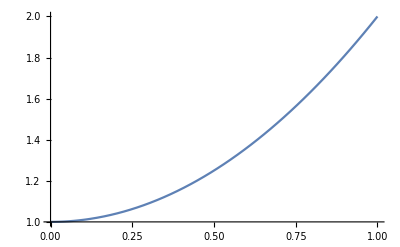

```mathematica
me=0.;
M=105.;
e=1.5
Enrg=300.;
Plot[x^2 +1,{x,0,1}]
```

```mathematica
Divide[%,1/e^4]
```

e^4 (cos^2(θ) (e^4-(e^4 M^2)/Enrg^2)+(e^4 M^2)/Enrg^2+e^4)

```mathematica
Distribute[1/e^4 Cos[θ]^2(e^4-(e^4 M^2)/Enrg^2)]+Distribute[1/e^4((e^4 M^2)/Enrg^2+e^4)]
```

-(M^2 cos^2(θ))/Enrg^2+M^2/Enrg^2+cos^2(θ)+1

```mathematica
W=Collect[%,Cos[θ]]
```

(1-M^2/Enrg^2) cos^2(θ)+M^2/Enrg^2+1

```mathematica
A^2(SuperPlus[e] SuperMinus[e]->SuperPlus[μ] SuperMinus[μ])==e^4*(W)
```

A^2 (e^- e^+→μ^- μ^+)==e^4 ((1-M^2/Enrg^2) cos^2(θ)+M^2/Enrg^2+1)

```mathematica
Cos[θ]^2 FullSimplify[(e^4-(e^4 M^2)/Enrg^2)]+FullSimplify[(e^4 M^2)/Enrg^2+e^4]
```

e^4 (1-M^2/Enrg^2) cos^2(θ)+e^4 (M^2/Enrg^2+1)

```mathematica
dσ/dΩ==1/(2 Subscript[E, A] 2 Subscript[E, B]|Subscript[v, A]-Subscript[v, B]|)(|Subscript[p, 1]|)/(4 π^2 4 Subscript[E, cm])A^2(Subscript[p, A] Subscript[p, B]->Subscript[p, 1] Subscript[p, 2])
```

```mathematica
dσ/dΩ==1/(2(Ec/2)2(Ec/2)|Subscript[v, A]-Subscript[v, B]|)(|Subscript[p, 1]|)/(4 π^2 4Ecm)A^2(p p'->k k')
```

dσ/dΩ==(A^2 |k| (p p'→k k'))/(16 π^2 Ec^2 Ecm |v_A-v_B|)

```mathematica
k=√(Enrg^2-M^2);
Subscript[v, A]-Subscript[v, B]=2;
```

```mathematica
dσ/dΩ==(|k|)/(32 π^2 Ecm^3)e^4((M^2/Enrg^2+1)+Cos[θ]^2(1-M^2/Enrg^2))
```

dσ/dΩ==(e^4 ((1-M^2/Enrg^2) cos^2(θ)+M^2/Enrg^2+1) |√(Enrg^2-M^2)|)/(32 π^2 Ecm^3)

```mathematica
e=√(4π α);
```

```mathematica
dσ/dΩ==(|k|)/(32 π^2 Ecm^3)e^4((M^2/Enrg^2+1)+Cos[θ]^2(1-M^2/Enrg^2))
```

dσ/dΩ==(α^2 ((1-M^2/Enrg^2) cos^2(θ)+M^2/Enrg^2+1) |√(Enrg^2-M^2)|)/(2 Ecm^3)

```mathematica
dσ/dΩ==PowerExpand[√(Enrg^2 Distribute[1/Enrg^2(Enrg^2-M^2)])]/(32 π^2 Ecm^3)e^4((M^2/Enrg^2+1)+Cos[θ]^2(1-M^2/Enrg^2))
```

dσ/dΩ==(α^2 Enrg √(1-M^2/Enrg^2) ((1-M^2/Enrg^2) cos^2(θ)+M^2/Enrg^2+1))/(2 Ecm^3)

```mathematica
Enrg-> Ecm/2;
```

```mathematica
dσ/dΩ==(Ecm/2 √(1-M^2/Enrg^2))/(32 π^2 Ecm^3)e^4((M^2/Enrg^2+1)+Cos[θ]^2(1-M^2/Enrg^2))
```

dσ/dΩ==(α^2 √(1-M^2/Enrg^2) ((1-M^2/Enrg^2) cos^2(θ)+M^2/Enrg^2+1))/(4 Ecm^2)

## Total Cross Section

```mathematica
σ==∫dσ==∫(α^2 √(1-M^2/Enrg^2) ((1-M^2/Enrg^2) cos^2(θ)+M^2/Enrg^2+1))/(4 Ecm^2)ⅆΩ==∫(α^2 √(1-M^2/Enrg^2) ((1-M^2/Enrg^2) cos^2(θ)+M^2/Enrg^2+1))/(4 Ecm^2)Sinθⅆθ dϕ==∫(α^2 √(1-M^2/Enrg^2) ((1-M^2/Enrg^2) cos^2(θ)+M^2/Enrg^2+1))/(4 Ecm^2)ⅆCosθ (2π)

(2π α^2)/(4 Ecm^2)∫√(1-M^2/Enrg^2) ((1-M^2/Enrg^2) cos^2(θ)+M^2/Enrg^2+1)ⅆCosθ==(2π α^2)/(4 Ecm^2)√(1-M^2/Enrg^2)(∫ ((1-M^2/Enrg^2) Cos[θ]^2)ⅆCosθ+∫(M^2/Enrg^2+1)ⅆCosθ)
```

```mathematica
(1-M^2/Enrg^2)Integrate[u^2,u ]
u=Cos[θ];
```

(1-M^2/Enrg^2) ∫cos^2(θ)ⅆcos(θ)

```mathematica
∫_0^π Cos[θ]^2 Sin[θ]ⅆθ
```

2/3

```mathematica
∫_0^π Sin[θ]ⅆθ
```

2

```mathematica
(2π α^2)/(4 Ecm^2)√(1-M^2/Enrg^2)((1-M^2/Enrg^2)∫_0^π Cos[θ]^2 Sin[θ]ⅆθ+(M^2/Enrg^2+1)∫_0^π Sin[θ]ⅆθ)
```

(π α^2 √(1-M^2/Enrg^2) (2/3 (1-M^2/Enrg^2)+2 (M^2/Enrg^2+1)))/(2 Ecm^2)

```mathematica
FullSimplify[(√(1-M^2/Enrg^2) (2/3 (1-M^2/Enrg^2)+2 (1+M^2/Enrg^2)) π α^2)/(2 Ecm^2)]
```

(2 π α^2 (2 Enrg^2+M^2) √(1-M^2/Enrg^2))/(3 Ecm^2 Enrg^2)

```mathematica
Subscript[σ, total]==(2 π α^2 2 Enrg^2(Distribute[1/(2 Enrg^2)(2 Enrg^2+M^2)]) √(1-M^2/Enrg^2))/(3 Ecm^2 Enrg^2)
```

σ_total==(4 π α^2 √(1-M^2/Enrg^2) (M^2/(2 Enrg^2)+1))/(3 Ecm^2)

```mathematica
At High Energies E>>M
```

```mathematica
a=(Series[√(1-(z)^2),{z,0,4}]*((1+1/2 z^2)))
```

1-(3 z^4)/8+O(z^5)

```mathematica
Subscript[σ, total]==(4 π α^2)/(3 Ecm^2)*a
z=M/Enrg;
```

σ_total==(4 π α^2 (1-3/8 (M/Enrg)^4+O((M/Enrg)^5)))/(3 Ecm^2)

## Condensed Calculation

```mathematica
Tr[(DiracMatrix[μ].(DiracSlash[p']-m)).(DiracMatrix[ν].(DiracSlash[p]+m))]*Tr[(DiracMatrix[μ].(DiracSlash[k]+M)).(DiracMatrix[ν].(DiracSlash[k']-M))]//Expand2//Factor1//Contract
```

32 m^2 (k̄·OverBar[k'])+32 (k̄·OverBar[p']) (p̄·OverBar[k'])+32 (k̄·p̄) (OverBar[k']·OverBar[p'])+32 M^2 (p̄·OverBar[p'])+64 m^2 M^2

```mathematica
AmpSquared=e^4/q^4 ChangeDimension[Tr[(DiracMatrix[μ].(DiracSlash[p']-m)).(DiracMatrix[ν].(DiracSlash[p]+m))]*Tr[(DiracMatrix[μ].(DiracSlash[k]+M)).(DiracMatrix[ν].(DiracSlash[k']-M))]//Expand2//Factor1//Contract//FermionSpinSum[#, ExtraFactor -> 1/4]&//ReplaceAll[#, DiracTrace :> Tr]&//Contract//Simplify,D]
```

(8 e^4 (m^2 (k·k')+(k·p') (p·k')+(k·p) (k'·p')+2 m^2 M^2+M^2 (p·p')))/q^4

```mathematica
AmpSquaredmasslesselec=(AmpSquared/.{m->0})//Simplify
```

(8 e^4 ((k·p') (p·k')+(k·p) (k'·p')+M^2 (p·p')))/q^4

```mathematica
AmpSquaredAllmassless=(AmpSquaredmasslesselec/.{M->0})//Simplify
```

(8 e^4 ((k·p') (p·k')+(k·p) (k'·p')))/q^4

```mathematica
|Subscript[v, A]-Subscript[v, B]|=2;
EA=EB=Ecm/2;
SPD[p',k']=SPD[p,k];
SPD[p',k]=SPD[p,k'];
SPD[p,k]= Enrg^2-Enrg k Cos[θ];
SPD[p,k']= Enrg^2+Enrg k Cos[θ];
SPD[p,p']= 2 Enrg^2;
q=(4 Enrg^2)^(1/2);
DiffCross=(d[Cos θ]dϕ)/(2EA 2 EB|Subscript[v, A]-Subscript[v, B]|)(|k|)/(4 π^2 4Ecm)*AmpSquaredmasslesselec//FullSimplify
```

(dϕ e^4 d(Cos θ) |k| (Enrg^2+k^2 cos^2(θ)+M^2))/(32 π^2 Ecm^3 Enrg^2)

```mathematica
|k|=k=√(Enrg^2-M^2);
```

```mathematica
DiffCross/(d[Cos θ]dϕ)
```

(e^4 √(Enrg^2-M^2) ((Enrg^2-M^2) cos^2(θ)+Enrg^2+M^2))/(32 π^2 Ecm^3 Enrg^2)

```mathematica
DiffCross/(d[Cos θ]dϕ)*(1/(Cos[θ]^2(Enrg^2- M^2)+M^2+Enrg^2))
```

(e^4 √(Enrg^2-M^2))/(32 π^2 Ecm^3 Enrg^2)

```mathematica
%*(Enrg^2*((1-M^2/Enrg^2)Cos[θ]^2+(1+M^2/Enrg^2)))
```

(e^4 √(Enrg^2-M^2) ((1-M^2/Enrg^2) cos^2(θ)+M^2/Enrg^2+1))/(32 π^2 Ecm^3)

```mathematica
Enrg=Ecm/2;
Enrg=.
e=√(4π α);
```

```mathematica
e=.
```

```mathematica
e^4 PowerExpand[√(Enrg^2*Distribute[1/Enrg^2(Enrg^2-M^2)])]/(32 π^2 Ecm^3)((M^2/Enrg^2+1)+Cos[θ]^2(1-M^2/Enrg^2))
```

(e^4 Enrg √(1-M^2/Enrg^2) ((1-M^2/Enrg^2) cos^2(θ)+M^2/Enrg^2+1))/(32 π^2 Ecm^3)

```mathematica
EnrgA=Ecm/2;
α^2(EnrgA √(1-M^2/Enrg^2))/(2 Ecm^3)((M^2/Enrg^2+1)+Cos[θ]^2(1-M^2/Enrg^2))
```

(α^2 √(1-M^2/Enrg^2) ((1-M^2/Enrg^2) cos^2(θ)+M^2/Enrg^2+1))/(4 Ecm^2)

```mathematica
Cos[θ]^2 Simplify[(Enrg^2- M^2)]+Expand[M^2+Enrg^2]
```

(Enrg^2-M^2) cos^2(θ)+Enrg^2+M^2

## FeynArts

```mathematica
$Language="English";
$LoadFeynArts=True;
$LoadFormCalc=True;
```

> Top. 1 aebe/cede/0.m, 0 diagrams

> Top. 2 aebe/cfdf/ef.m, 0 diagrams

> Top. 3 aebf/cedf/ef.m, 0 diagrams

> Top. 4 aebf/cfde/ef.m, 0 diagrams



FeynArtsGraphics(2→2)(([T1] | [T2] | [T3]
[T4] | Null | Null
Null | Null | Null))

```mathematica
S1=CreateTopologies[0, 2 -> 2];
Paint[%]
```

## e^-e^+→μ^-μ^+ (Momenta terms and Mandelstam)

loading generic model file /Users/asight4soreyes/Library/Mathematica/Applications/FeynCalc/FeynArts/Models/Lorentz.gen

> $GenericMixing is OFF

generic model {Lorentz} initialized

loading classes model file /Users/asight4soreyes/Library/Mathematica/Applications/FeynCalc/FeynArts/Models/SM.mod

$CKM=False

> 46 particles (incl. antiparticles) in 16 classes

> $CounterTerms are ON

> 88 vertices

> 115 counterterms of order 1

> 6 counterterms of order 2

classes model {SM} initialized

Excluding 0 Generic, 3 Classes, and 3 Particles fields

inserting at level(s) {Classes}

> Top. 1: 0 Classes insertions

> Top. 2: 1 Classes insertion

> Top. 3: 0 Classes insertions

> Top. 4: 0 Classes insertions

Restoring 0 Generic, 3 Classes, and 3 Particles fields

in total: 1 Classes insertion

> Top. 1 aebe/cfdf/ef.m, 0 diagrams

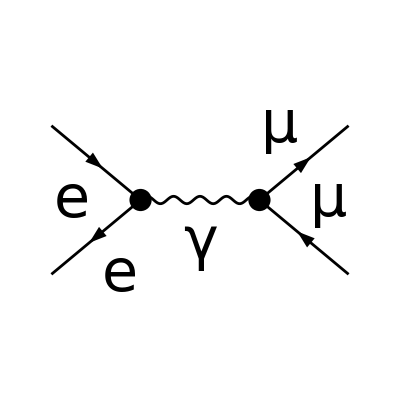

```mathematica
T1=CreateTopologies[0, 2 -> 2];
diagt1 = InsertFields[T1, {F[2, {1}], -F[2, {1}]} ->
		{F[2, {2}], -F[2, {2}]}, InsertionLevel -> {Classes},
		Model -> "SM", ExcludeParticles -> {S[1], S[2], V[2]}];
Paint[diagt1, ColumnsXRows -> {1, 1}, Numbering -> None,SheetHeader->None,ImageSize->{512,512}];
```

```mathematica
A = FCFAConvert[CreateFeynAmp[diagt1, Truncated -> False],
IncomingMomenta->{p,p'},OutgoingMomenta->{k,k'},UndoChiralSplittings->True,
ChangeDimension->4,List->False,SMP->True]
```

((ḡ)^Lor1Lor2 (φ(-OverBar[p'],m_e)).(ⅈ e (γ̄)^Lor1).(φ(p̄,m_e)) (φ(k̄,m_μ)).(ⅈ e (γ̄)^Lor2).(φ(-OverBar[k'],m_μ)))/(OverBar[k']+k̄)^2

```mathematica
ComplexConjugate[A]
```

-(e^2 (ḡ)^Lor1Lor2 (φ(p̄,m_e)).(γ̄)^Lor1.(φ(-OverBar[p'],m_e)) (φ(-OverBar[k'],m_μ)).(γ̄)^Lor2.(φ(k̄,m_μ)))/(OverBar[k']+k̄)^2

```mathematica
sqAmptest= (A (ComplexConjugate[A]//FCRenameDummyIndices))//
		PropagatorDenominatorExplicit//Contract//FermionSpinSum[#, ExtraFactor -> 1/4]&//
		ReplaceAll[#, DiracTrace :> Tr]&//Contract
```

(16 e^4 m_e^2 m_μ^2)/((OverBar[k']^2+2 (k̄·OverBar[k'])+(k̄)^2)^2)+(8 e^4 m_e^2 (k̄·OverBar[k']))/((OverBar[k']^2+2 (k̄·OverBar[k'])+(k̄)^2)^2)+(8 e^4 m_μ^2 (p̄·OverBar[p']))/((OverBar[k']^2+2 (k̄·OverBar[k'])+(k̄)^2)^2)+(8 e^4 (k̄·p̄) (OverBar[k']·OverBar[p']))/((OverBar[k']^2+2 (k̄·OverBar[k'])+(k̄)^2)^2)+(8 e^4 (k̄·OverBar[p']) (p̄·OverBar[k']))/((OverBar[k']^2+2 (k̄·OverBar[k'])+(k̄)^2)^2)

```mathematica
sqAmp = (A (ComplexConjugate[A]//FCRenameDummyIndices))//
		PropagatorDenominator//Contract//FermionSpinSum[#, ExtraFactor -> 1/4]&//
		ReplaceAll[#, DiracTrace :> Tr]&//Contract//FullSimplify
```

DiracSimplify::spinorsleft: Error! After applying FermionSpinSum to all spinor chains the output
still contains spinors. Evaluation aborted.

1/4 1/(e^8 (1/(OverBar[k']+k̄)^2)^4 ((φ(-OverBar[p'],m_e)).(γ̄)^Lor1.(φ(p̄,m_e)))^2 ((φ(k̄,m_μ)).(γ̄)^Lor1.(φ(-OverBar[k'],m_μ)))^2 ((φ(p̄,m_e)).(γ̄)^($AL($30)).(φ(-OverBar[p'],m_e)))^2 ((φ(-OverBar[k'],m_μ)).(γ̄)^($AL($30)).(φ(k̄,m_μ)))^2)

```mathematica
masslessElectronssqAmp= (sqAmp/. {SMP["m_e"] -> 0})//FullSimplify
```

(8 e^4 ((k̄·OverBar[p']) (p̄·OverBar[k'])+(k̄·p̄) (OverBar[k']·OverBar[p'])+m_μ^2 (p̄·OverBar[p'])))/((OverBar[k']^2+2 (k̄·OverBar[k'])+(k̄)^2)^2)

```mathematica
masslessElecMuonsqAmp= (masslessElectronssqAmp/. {SMP["m_mu"] -> 0})//Simplify
```

(8 e^4 ((k̄·OverBar[p']) (p̄·OverBar[k'])+(k̄·p̄) (OverBar[k']·OverBar[p'])))/((OverBar[k']^2+2 (k̄·OverBar[k'])+(k̄)^2)^2)

```mathematica
SetMandelstam[s, t, u, p, p', -k, -k', SMP["m_e"], SMP["m_e"], SMP["m_mu"], SMP["m_mu"]];
```

```mathematica
masslessElectronssqAmp= (sqAmp/. {SMP["m_e"] -> 0})//FullSimplify
```

(2 e^4 (2 m_μ^4-2 m_μ^2 (-s+t+u)+t^2+u^2))/s^2

```mathematica
masslessElecMuonsqAmp= (masslessElectronssqAmp/. {SMP["m_mu"] -> 0})//Simplify
```

(2 e^4 (t^2+u^2))/s^2

## e^-e^+→μ^-μ^+ (Alternate 1)

loading generic model file /Users/asight4soreyes/Library/Mathematica/Applications/FeynCalc/FeynArts/Models/Lorentz.gen

> $GenericMixing is OFF

generic model {Lorentz} initialized

loading classes model file /Users/asight4soreyes/Library/Mathematica/Applications/FeynCalc/FeynArts/Models/SM.mod

$CKM=False

> 46 particles (incl. antiparticles) in 16 classes

> $CounterTerms are ON

> 88 vertices

> 115 counterterms of order 1

> 6 counterterms of order 2

classes model {SM} initialized

Excluding 0 Generic, 3 Classes, and 3 Particles fields

inserting at level(s) {Classes}

> Top. 1: 0 Classes insertions

> Top. 2: 1 Classes insertion

> Top. 3: 0 Classes insertions

> Top. 4: 0 Classes insertions

Restoring 0 Generic, 3 Classes, and 3 Particles fields

in total: 1 Classes insertion

> Top. 1 aebe/cfdf/ef.m, 0 diagrams

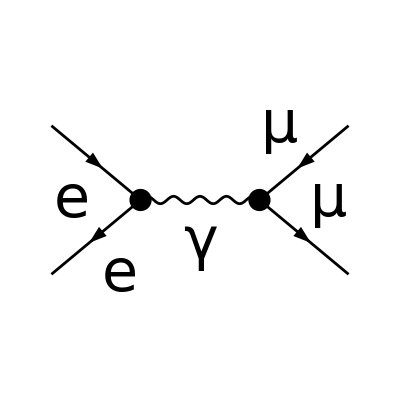

```mathematica
T2=CreateTopologies[0, 2 -> 2];
diagt2 = InsertFields[T2, {F[2, {1}], -F[2, {1}]} ->
		{-F[2, {2}], F[2, {2}]}, InsertionLevel -> {Classes},
		Model -> "SM", ExcludeParticles -> {S[1], S[2], V[2]}];
Paint[diagt2, ColumnsXRows -> {1, 1}, Numbering -> None,SheetHeader->None,ImageSize->{512,512}];
```

```mathematica
B = FCFAConvert[CreateFeynAmp[diagt2, Truncated -> False],
IncomingMomenta->{p,p'},OutgoingMomenta->{k,k'},UndoChiralSplittings->True,
ChangeDimension->4,List->False,SMP->True]
```

creating amplitudes at level(s) {Classes}

> Top. 1: 1 Classes amplitude

in total: 1 Classes amplitude

-((ḡ)^Lor1Lor2 (φ(-OverBar[p'],m_e)).(ⅈ e (γ̄)^Lor1).(φ(p̄,m_e)) (φ(OverBar[k'],m_μ)).(ⅈ e (γ̄)^Lor2).(φ(-k̄,m_μ)))/(OverBar[k']+k̄)^2

```mathematica
SetMandelstam[s, t, u, p, p', -k, -k', SMP["m_e"], SMP["m_e"], SMP["m_mu"], SMP["m_mu"]];
sqAmp2 = (B(ComplexConjugate[B]//FCRenameDummyIndices))//
		PropagatorDenominatorExplicit//Contract//FermionSpinSum[#, ExtraFactor -> 1/4]&//
		ReplaceAll[#, DiracTrace :> Tr]&//Contract//Simplify
```

(2 e^4 (2 m_e^2 (2 m_μ^2+s-t-u)+2 m_e^4+2 m_μ^4+2 m_μ^2 (s-t-u)+t^2+u^2))/s^2

```mathematica
masslessElectronssqAmp2= (sqAmp2/. {SMP["m_e"] -> 0})//Simplify
```

(2 e^4 (2 m_μ^4+2 m_μ^2 (s-t-u)+t^2+u^2))/s^2

```mathematica
masslessElecMuonsqAmp2= (masslessElectronssqAmp2/. {SMP["m_mu"] -> 0})//Simplify
```

(2 e^4 (t^2+u^2))/s^2

## e^-e^+→μ^-μ^+ (Alternate 2)

```mathematica
T3=CreateTopologies[0, 2 -> 2];
diagt3 = InsertFields[T3, {F[2, {1}], -F[2, {1}]} ->
		{F[2, {2}], -F[2, {2}]}, InsertionLevel -> {Classes},
		Model -> "SM", ExcludeParticles -> {S[1], S[2], V[2]}];
Paint[diagt3, ColumnsXRows -> {1, 1}, Numbering -> None,SheetHeader->None,ImageSize->{512,512}];
```

loading generic model file /Users/asight4soreyes/Library/Mathematica/Applications/FeynCalc/FeynArts/Models/Lorentz.gen

> $GenericMixing is OFF

generic model {Lorentz} initialized

loading classes model file /Users/asight4soreyes/Library/Mathematica/Applications/FeynCalc/FeynArts/Models/SM.mod

$CKM=False

> 46 particles (incl. antiparticles) in 16 classes

> $CounterTerms are ON

> 88 vertices

> 115 counterterms of order 1

> 6 counterterms of order 2

classes model {SM} initialized

Excluding 0 Generic, 3 Classes, and 3 Particles fields

inserting at level(s) {Classes}

> Top. 1: 0 Classes insertions

> Top. 2: 1 Classes insertion

> Top. 3: 0 Classes insertions

> Top. 4: 0 Classes insertions

Restoring 0 Generic, 3 Classes, and 3 Particles fields

in total: 1 Classes insertion

> Top. 1 aebe/cfdf/ef.m, 0 diagrams

-Graphics-

```mathematica
H = FCFAConvert[CreateFeynAmp[diagt3, Truncated -> False],
IncomingMomenta->{p,p'},OutgoingMomenta->{k,k'},UndoChiralSplittings->True,
ChangeDimension->4,List->False,SMP->True]
```

creating amplitudes at level(s) {Classes}

> Top. 1: 1 Classes amplitude

in total: 1 Classes amplitude

((ḡ)^Lor1Lor2 (φ(-OverBar[p'],m_e)).(ⅈ e (γ̄)^Lor1).(φ(p̄,m_e)) (φ(k̄,m_μ)).(ⅈ e (γ̄)^Lor2).(φ(-OverBar[k'],m_μ)))/(OverBar[k']+k̄)^2

```mathematica
SetMandelstam[s, t, u, p, p', -k, -k', SMP["m_e"], SMP["m_mu"], SMP["m_e"], SMP["m_mu"]];
sqAmp3 = (H(ComplexConjugate[H]//FCRenameDummyIndices))//
		PropagatorDenominatorExplicit//Contract//FermionSpinSum[#, ExtraFactor -> 1/4]&//
		ReplaceAll[#, DiracTrace :> Tr]&//Contract//Simplify
```

(2 e^4 (2 m_e^2 (5 m_μ^2+s-t-u)-m_e^4-m_μ^4+2 m_μ^2 (s-t-u)+t^2+u^2))/s^2

```mathematica
masslessElectronssqAmp3= (sqAmp3/. {SMP["m_e"] -> 0})//Simplify
```

(2 e^4 (-m_μ^4+2 m_μ^2 (s-t-u)+t^2+u^2))/s^2

```mathematica
masslessElecMuonsqAmp3= (masslessElectronssqAmp3/. {SMP["m_mu"] -> 0})//Simplify
```

(2 e^4 (t^2+u^2))/s^2

## e^-e^+→μ^-μ^+ (Alternate 3)

```mathematica
T4=CreateTopologies[0, 2 -> 2];
diagt4 = InsertFields[T4, {F[2, {1}], -F[2, {1}]} ->
		{-F[2, {2}], F[2, {2}]}, InsertionLevel -> {Classes},
		Model -> "SM", ExcludeParticles -> {S[1], S[2], V[2]}];
Paint[diagt4, ColumnsXRows -> {1, 1}, Numbering -> None,SheetHeader->None,ImageSize->{512,512}];
```

loading generic model file /Users/asight4soreyes/Library/Mathematica/Applications/FeynCalc/FeynArts/Models/Lorentz.gen

> $GenericMixing is OFF

generic model {Lorentz} initialized

loading classes model file /Users/asight4soreyes/Library/Mathematica/Applications/FeynCalc/FeynArts/Models/SM.mod

$CKM=False

> 46 particles (incl. antiparticles) in 16 classes

> $CounterTerms are ON

> 88 vertices

> 115 counterterms of order 1

> 6 counterterms of order 2

classes model {SM} initialized

Excluding 0 Generic, 3 Classes, and 3 Particles fields

inserting at level(s) {Classes}

> Top. 1: 0 Classes insertions

> Top. 2: 1 Classes insertion

> Top. 3: 0 Classes insertions

> Top. 4: 0 Classes insertions

Restoring 0 Generic, 3 Classes, and 3 Particles fields

in total: 1 Classes insertion

> Top. 1 aebe/cfdf/ef.m, 0 diagrams

-Graphics-

```mathematica
J = FCFAConvert[CreateFeynAmp[diagt4, Truncated -> False],
IncomingMomenta->{p,p'},OutgoingMomenta->{k,k'},UndoChiralSplittings->True,
ChangeDimension->4,List->False,SMP->True]
```

creating amplitudes at level(s) {Classes}

> Top. 1: 1 Classes amplitude

in total: 1 Classes amplitude

-((ḡ)^Lor1Lor2 (φ(-OverBar[p'],m_e)).(ⅈ e (γ̄)^Lor1).(φ(p̄,m_e)) (φ(OverBar[k'],m_μ)).(ⅈ e (γ̄)^Lor2).(φ(-k̄,m_μ)))/(OverBar[k']+k̄)^2

```mathematica
SetMandelstam[s, t, u, p, p', -k, -k', SMP["m_e"], SMP["m_mu"], SMP["m_e"], SMP["m_mu"]];
sqAmp4 = (J(ComplexConjugate[J]//FCRenameDummyIndices))//
		PropagatorDenominatorExplicit//Contract//FermionSpinSum[#, ExtraFactor -> 1/4]&//
		ReplaceAll[#, DiracTrace :> Tr]&//Contract//Simplify
```

(2 e^4 (2 m_e^2 (5 m_μ^2+s-t-u)-m_e^4-m_μ^4+2 m_μ^2 (s-t-u)+t^2+u^2))/s^2

```mathematica
masslessElectronssqAmp4= (sqAmp4/. {SMP["m_e"] -> 0})//Simplify
```

(2 e^4 (-m_μ^4+2 m_μ^2 (s-t-u)+t^2+u^2))/s^2

```mathematica
masslessElecMuonsqAmp4= (masslessElectronssqAmp4/. {SMP["m_mu"] -> 0})//Simplify
```

(2 e^4 (t^2+u^2))/s^2

```mathematica
.00*.00.00
```

```mathematica
S1=CreateTopologies[0, 2 -> 2];
Paint[%]
```

> Top. 1 aebe/cede/0.m, 0 diagrams

> Top. 2 aebe/cfdf/ef.m, 0 diagrams

> Top. 3 aebf/cedf/ef.m, 0 diagrams

> Top. 4 aebf/cfde/ef.m, 0 diagrams

-Graphics-

FeynArtsGraphics(2→2)(([T1] | [T2] | [T3]
[T4] | Null | Null
Null | Null | Null))

```mathematica
Diagrams=InsertFields[S1,{F[2,{1}],-F[2,{1}]}->{F[2,{1}],-F[2,{1}]},InsertionLevel->{Classes}];
```

inserting at level(s) {Classes}

> Top. 1: 0 Classes insertions

> Top. 2: 4 Classes insertions

> Top. 3: 4 Classes insertions

> Top. 4: 0 Classes insertions

in total: 8 Classes insertions

> Top. 1 aebe/cfdf/ef.m, 0 diagrams

> Top. 2 aebf/cedf/ef.m, 0 diagrams

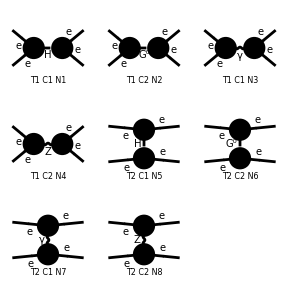

FeynArtsGraphics({e,e}→{e,e})(([T1 C1 N1] | [T1 C2 N2] | [T1 C1 N3]
[T1 C2 N4] | [T2 C1 N5] | [T2 C2 N6]
[T2 C1 N7] | [T2 C2 N8] | Null))

```mathematica
Paint[%]
```

Excluding 0 Generic, 3 Classes, and 3 Particles fields

inserting at level(s) {Classes}

> Top. 1: 0 Classes insertions

> Top. 2: 1 Classes insertion

> Top. 3: 1 Classes insertion

> Top. 4: 0 Classes insertions

Restoring 0 Generic, 3 Classes, and 3 Particles fields

in total: 2 Classes insertions

> Top. 1 aebe/cfdf/ef.m, 0 diagrams

> Top. 2 aebf/cedf/ef.m, 0 diagrams

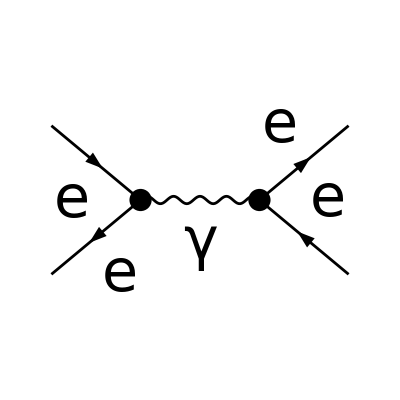

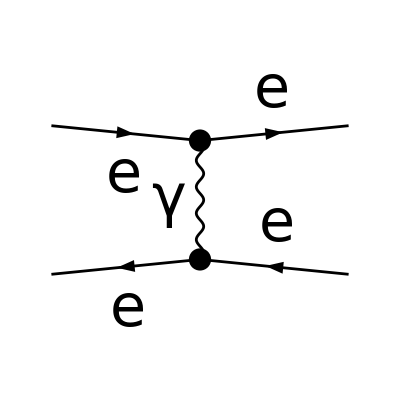

```mathematica
s1=CreateTopologies[0, 2 -> 2];
diags1 = InsertFields[s1, {F[2, {1}], -F[2, {1}]} ->
		{F[2, {1}], -F[2, {1}]}, InsertionLevel -> {Classes},
		Model -> "SM", ExcludeParticles -> {S[1], S[2], V[2]}];
Paint[diags1, ColumnsXRows -> {1, 1}, Numbering -> None,SheetHeader->None,ImageSize->{512,512}];
```

```mathematica
B = FCFAConvert[CreateFeynAmp[diags1, Truncated -> False],
IncomingMomenta->{p,p'},OutgoingMomenta->{k,k'},UndoChiralSplittings->True,
ChangeDimension->4,List->False,SMP->True]
```

creating amplitudes at level(s) {Classes}

> Top. 1: 1 Classes amplitude

> Top. 2: 1 Classes amplitude

in total: 2 Classes amplitudes

((ḡ)^Lor1Lor2 (φ(k̄,m_e)).(ⅈ e (γ̄)^Lor2).(φ(-OverBar[k'],m_e)) (φ(-OverBar[p'],m_e)).(ⅈ e (γ̄)^Lor1).(φ(p̄,m_e)))/(OverBar[k']+k̄)^2-((ḡ)^Lor1Lor2 (φ(k̄,m_e)).(ⅈ e (γ̄)^Lor1).(φ(p̄,m_e)) (φ(-OverBar[p'],m_e)).(ⅈ e (γ̄)^Lor2).(φ(-OverBar[k'],m_e)))/(OverBar[k']-OverBar[p'])^2

```mathematica
SetMandelstam[s, t, u, p, p', -k, -k', SMP["m_e"], SMP["m_e"], SMP["m_e"], SMP["m_e"]];
sqAmp1 = (B(ComplexConjugate[B]//FCRenameDummyIndices))//
		PropagatorDenominatorExplicit//Contract//FermionSpinSum[#, ExtraFactor -> 1/4]&//
		ReplaceAll[#, DiracTrace :> Tr]&//Contract//FullSimplify
```

(2 e^4 (8 m_e^4 (s^2+s t+t^2)-4 m_e^2 (s^3+s^2 (u-2 t)+s t (3 u-2 t)+t^2 (t+u))+s^4+u^2 (s+t)^2+t^4))/(s^2 t^2)

```mathematica
masslessElectronssqAmp1= (sqAmp1/. {SMP["m_e"] -> 0})//Simplify
```

(2 e^4 (s^4+u^2 (s+t)^2+t^4))/(s^2 t^2)

```mathematica
e=√(4π α);
α=α
```

α

```mathematica
(2 (e)^4 (s^4+u^2 (s+t)^2+t^4))/(s^2 t^2)
```

(32 π^2 α^2 (s^4+u^2 (s+t)^2+t^4))/(s^2 t^2)

```mathematica
v=%
```

(32 π^2 α^2 (s^4+u^2 (s+t)^2+t^4))/(s^2 t^2)

```mathematica
w=(32 (π^2) (α^2))((u^2 (Simplify[(s+t)/(s t)])^2)+(s^4/(s^2 t^2)+t^4/(s^2 t^2)))
```

32 π^2 α^2 (s^2/t^2+t^2/s^2+u^2 (1/s+1/t)^2)

```mathematica
v-w
```

(32 π^2 α^2 (s^4+u^2 (s+t)^2+t^4))/(s^2 t^2)-32 π^2 α^2 (s^2/t^2+t^2/s^2+u^2 (1/s+1/t)^2)

```mathematica
Simplify[-32 π^2 (s^2/t^2+t^2/s^2+(1/s+1/t)^2 u^2) α^2+(32 π^2 (s^4+t^4+(s+t)^2 u^2) α^2)/(s^2 t^2)]
```

0

```mathematica
v==w
```

(32 π^2 α^2 (s^4+u^2 (s+t)^2+t^4))/(s^2 t^2)==32 π^2 α^2 (s^2/t^2+t^2/s^2+u^2 (1/s+1/t)^2)

```mathematica
True
```

```mathematica
masslessElectronsSqAmpElMuScatPeskin1= (8SMP["e"]^4 (SP[p,k']SP[p',k]+SP[p,p']SP[k,k']-
		SMP["m_mu"]^2 SP[p,k]))/(SP[k-p])^2
```

(8 e^4 ((-m_e^2/2-m_μ^2/2+s/2)^2+m_μ^2 (-(m_e^2-t/2))+(m_e^2/2+m_μ^2/2-u/2)^2))/(((k̄-p̄)^2)^2)

```mathematica
(2 SMP["e"]^4 (s^2+u^2-2 (s-t+u) SMP["m_mu"]^2+2 SMP["m_mu"]^4))/t^2
```

(2 e^4 (2 m_μ^4-2 m_μ^2 (s-t+u)+s^2+u^2))/t^2

```mathematica
Collect2[%,s]
```

(2 e^4 (t^2+u^2))/s^2+(2 e^4 s^2)/t^2+(4 e^4 u^2)/(s t)+(2 e^4 u^2)/t^2

```mathematica
Collect2[%,u]
```

(2 e^4 u^2 (s+t)^2)/(s^2 t^2)+(2 e^4 (s^4+t^4))/(s^2 t^2)

```mathematica
e=√(4π α)
```

2 √π √α

```mathematica
α=α
```

α

```mathematica
(2 (e)^4 (s^4+u^2 (s+t)^2+t^4))/(s^2 t^2)//Expand
```

(32 π^2 α^2 t^2)/s^2+(32 π^2 α^2 s^2)/t^2+(32 π^2 α^2 u^2)/s^2+(64 π^2 α^2 u^2)/(s t)+(32 π^2 α^2 u^2)/t^2

```mathematica
Collect2[%,u]
```

(32 π^2 α^2 u^2 (s+t)^2)/(s^2 t^2)+(32 π^2 α^2 (s^4+t^4))/(s^2 t^2)

```mathematica
Collect[%,32 π^2 α^2]
```

32 π^2 α^2 ((u^2 (s+t)^2)/(s^2 t^2)+(s^4+t^4)/(s^2 t^2))

```mathematica
(32 (π^2) (α^2))((u^2 ((s+t)/(s t))^2)+(s^4/(s^2 t^2)+t^4/(s^2 t^2)))
```

32 π^2 α^2 ((u^2 (s+t)^2)/(s^2 t^2)+s^2/t^2+t^2/s^2)

```mathematica
s=2 Enrg^2
t=-2 p^2(1-Cos[θ])
u=-2 p^2(1+Cos[θ])
```

2 Enrg^2

-2 p^2 (1-cos(θ))

-2 p^2 (cos(θ)+1)

```mathematica
(32 (π^2) (α^2))((u^2 ((s+t)/(s t))^2)+(s^4/(s^2 t^2)+t^4/(s^2 t^2)))
```

32 π^2 α^2 (Enrg^4/(p^4 (1-cos(θ))^2)+(p^4 (1-cos(θ))^2)/Enrg^4+((cos(θ)+1)^2 (2 Enrg^2-2 p^2 (1-cos(θ)))^2)/(4 Enrg^4 (1-cos(θ))^2))

```mathematica
Collect[%,p^4]
```

(32 π^2 α^2 (cos(θ)+1)^2)/(1-cos(θ))^2+(32 π^2 α^2 Enrg^4)/(p^4 (1-cos(θ))^2)+32 π^2 α^2 p^4 ((1-cos(θ))^2/Enrg^4+(cos(θ)+1)^2/Enrg^4)-(64 π^2 α^2 p^2 (cos(θ)+1)^2)/(Enrg^2 (1-cos(θ)))

```mathematica
<<FormCalc`
```

FeynAmp::shdw: Symbol FeynAmp appears in multiple contexts {FeynArts`,FeynCalc`}; definitions in context FeynArts` may shadow or be shadowed by other definitions.

FeynAmpList::shdw: Symbol FeynAmpList appears in multiple contexts {FeynArts`,FeynCalc`}; definitions in context FeynArts` may shadow or be shadowed by other definitions.

GaugeXi::shdw: Symbol GaugeXi appears in multiple contexts {FeynArts`,FeynCalc`}; definitions in context FeynArts` may shadow or be shadowed by other definitions.

PropagatorDenominator::shdw: Symbol PropagatorDenominator appears in multiple contexts {FeynArts`,FeynCalc`}; definitions in context FeynArts` may shadow or be shadowed by other definitions.

FeynAmpDenominator::shdw: Symbol FeynAmpDenominator appears in multiple contexts {FeynArts`,FeynCalc`}; definitions in context FeynArts` may shadow or be shadowed by other definitions.

NonCommutative::shdw: Symbol NonCommutative appears in multiple contexts {FeynArts`,FeynCalc`}; definitions in context FeynArts` may shadow or be shadowed by other definitions.

LeviCivita::shdw: Symbol LeviCivita appears in multiple contexts {FeynArts`,FeynCalc`}; definitions in context FeynArts` may shadow or be shadowed by other definitions.

A0::shdw: Symbol A0 appears in multiple contexts {LoopTools`,FeynCalc`}; definitions in context LoopTools` may shadow or be shadowed by other definitions.

A00::shdw: Symbol A00 appears in multiple contexts {LoopTools`,FeynCalc`}; definitions in context LoopTools` may shadow or be shadowed by other definitions.

B0::shdw: Symbol B0 appears in multiple contexts {LoopTools`,FeynCalc`}; definitions in context LoopTools` may shadow or be shadowed by other definitions.

B1::shdw: Symbol B1 appears in multiple contexts {LoopTools`,FeynCalc`}; definitions in context LoopTools` may shadow or be shadowed by other definitions.

B00::shdw: Symbol B00 appears in multiple contexts {LoopTools`,FeynCalc`}; definitions in context LoopTools` may shadow or be shadowed by other definitions.

B11::shdw: Symbol B11 appears in multiple contexts {LoopTools`,FeynCalc`}; definitions in context LoopTools` may shadow or be shadowed by other definitions.

DB0::shdw: Symbol DB0 appears in multiple contexts {LoopTools`,FeynCalc`}; definitions in context LoopTools` may shadow or be shadowed by other definitions.

DB1::shdw: Symbol DB1 appears in multiple contexts {LoopTools`,FeynCalc`}; definitions in context LoopTools` may shadow or be shadowed by other definitions.

C0::shdw: Symbol C0 appears in multiple contexts {LoopTools`,FeynCalc`}; definitions in context LoopTools` may shadow or be shadowed by other definitions.

D0::shdw: Symbol D0 appears in multiple contexts {LoopTools`,FeynCalc`}; definitions in context LoopTools` may shadow or be shadowed by other definitions.

PaVe::shdw: Symbol PaVe appears in multiple contexts {LoopTools`,FeynCalc`}; definitions in context LoopTools` may shadow or be shadowed by other definitions.

Spinor::shdw: Symbol Spinor appears in multiple contexts {FormCalc`,FeynCalc`}; definitions in context FormCalc` may shadow or be shadowed by other definitions.

SUNN::shdw: Symbol SUNN appears in multiple contexts {FormCalc`,FeynCalc`}; definitions in context FormCalc` may shadow or be shadowed by other definitions.

DotExpand::shdw: Symbol DotExpand appears in multiple contexts {FormCalc`,FeynCalc`}; definitions in context FormCalc` may shadow or be shadowed by other definitions.

Dimension::shdw: Symbol Dimension appears in multiple contexts {FormCalc`,FeynCalc`}; definitions in context FormCalc` may shadow or be shadowed by other definitions.

PaVeReduce::shdw: Symbol PaVeReduce appears in multiple contexts {FormCalc`,FeynCalc`}; definitions in context FormCalc` may shadow or be shadowed by other definitions.

Pair::shdw: Symbol Pair appears in multiple contexts {FormCalc`,FeynCalc`}; definitions in context FormCalc` may shadow or be shadowed by other definitions.

Eps::shdw: Symbol Eps appears in multiple contexts {FormCalc`,FeynCalc`}; definitions in context FormCalc` may shadow or be shadowed by other definitions.

FCPrint::shdw: Symbol FCPrint appears in multiple contexts {FormCalc`,FeynCalc`}; definitions in context FormCalc` may shadow or be shadowed by other definitions.

DotSimplify::shdw: Symbol DotSimplify appears in multiple contexts {FormCalc`,FeynCalc`}; definitions in context FormCalc` may shadow or be shadowed by other definitions.

Combine::shdw: Symbol Combine appears in multiple contexts {FormCalc`,FeynCalc`}; definitions in context FormCalc` may shadow or be shadowed by other definitions.

PolarizationSum::shdw: Symbol PolarizationSum appears in multiple contexts {FormCalc`,FeynCalc`}; definitions in context FormCalc` may shadow or be shadowed by other definitions.

FinalFunction::shdw: Symbol FinalFunction appears in multiple contexts {FormCalc`,FeynCalc`}; definitions in context FormCalc` may shadow or be shadowed by other definitions.

DirectoryName::string: String expected at position 1 in DirectoryName[File].

ToFileName::strse: String or list of strings expected at position 1 in ToFileName[{DirectoryName[File],FormCalc}].

ToFileName::strse: String or list of strings expected at position 1 in ToFileName[{DirectoryName[File],MacOSX-x86-64}].

ToFileName::strse: String or list of strings expected at position 1 in ToFileName[{DirectoryName[File],drivers}].

General::stop: Further output of ToFileName::strse will be suppressed during this calculation.

FormCalc 9.6 (16 Apr 2018)

by Thomas Hahn

StringJoin::string: String expected at position 1 in ToFileName[ToFileName[{DirectoryName[File],MacOSX-x86-64}],tform]<>|-w2.

StringJoin::string: String expected at position \!\(\*FormBox["2", TraditionalForm]\) in \!\(\*FormBox[RowBox[{"\"\\\"\"", "<>", RowBox[{"ToFileName", "[", RowBox[{RowBox[{"ToFileName", "[", RowBox[{"{", RowBox[{RowBox[{"DirectoryName", "[", "File", "]"}], ",", "\"MacOSX-x86-64\""}], "}"}], "]"}], ",", "\"ToForm\""}], "]"}], "<>", "\"\\\"\""}], TraditionalForm]\).

StringJoin::string: String expected at position \!\(\*FormBox["2", TraditionalForm]\) in \!\(\*FormBox[RowBox[{"\"!\\\"\"", "<>", RowBox[{"ToFileName", "[", RowBox[{RowBox[{"ToFileName", "[", RowBox[{"{", RowBox[{RowBox[{"DirectoryName", "[", "File", "]"}], ",", "\"MacOSX-x86-64\""}], "}"}], "]"}], ",", "\"ToForm\""}], "]"}], "<>", "\"\\\" > \""}], TraditionalForm]\).

General::stop: Further output of \!\(\*FormBox[StyleBox[RowBox[{"StringJoin", "::", "string"}], "MessageName"], TraditionalForm]\) will be suppressed during this calculation.

Momentum::shdw: Symbol \!\(\*FormBox["\"Momentum\"", TraditionalForm]\) appears in multiple contexts \!\(\*FormBox[RowBox[{"{", RowBox[{"\"Global`\"", ",", "\"FeynCalc`\""}], "}"}], TraditionalForm]\); definitions in context \!\(\*FormBox["\"Global`\"", TraditionalForm]\) may shadow or be shadowed by other definitions.

Lor1::shdw: Symbol \!\(\*FormBox["\"Lor1\"", TraditionalForm]\) appears in multiple contexts \!\(\*FormBox[RowBox[{"{", RowBox[{"\"FormCalc`\"", ",", "\"Global`\""}], "}"}], TraditionalForm]\); definitions in context \!\(\*FormBox["\"FormCalc`\"", TraditionalForm]\) may shadow or be shadowed by other definitions.

Lor2::shdw: Symbol \!\(\*FormBox["\"Lor2\"", TraditionalForm]\) appears in multiple contexts \!\(\*FormBox[RowBox[{"{", RowBox[{"\"FormCalc`\"", ",", "\"Global`\""}], "}"}], TraditionalForm]\); definitions in context \!\(\*FormBox["\"FormCalc`\"", TraditionalForm]\) may shadow or be shadowed by other definitions.

Get::stream: \!\(\*FormBox[RowBox[{"ToFileName", "[", RowBox[{RowBox[{"ToFileName", "[", RowBox[{"{", RowBox[{RowBox[{"DirectoryName", "[", "File", "]"}], ",", "\"FormCalc\""}], "}"}], "]"}], ",", "\"ModelSpecific.m\""}], "]"}], TraditionalForm]\) is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

```mathematica
ClearProcess[];
A=CalcFeynAmp[CreateFeynAmp[Diagrams],FermionChains->VA];
matrix=SquaredME[amplitude]//.HelicityME[amplitude]
```

creating amplitudes at level(s) {Classes}

> Top. 1: 1 Classes amplitude

in total: 1 Classes amplitude

ReplaceRepeated::reps: {HelicityME(amplitude)} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

SquaredME(amplitude)//.HelicityME(amplitude)

```mathematica
Exit[]
```